```mathematica
(*QHA coupling to Tel data*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/RESULTS_QHA_Tel"];
qhatel={"300/Cp-temperature.dat","300/bulk_modulus-temperature.dat","300/gruneisen-temperature.dat","300/thermal_expansion.dat","1900/Cp-temperature.dat","1900/bulk_modulus-temperature.dat","1900/gruneisen-temperature.dat","1900/thermal_expansion.dat","3200/Cp-temperature.dat","3200/bulk_modulus-temperature.dat","3200/gruneisen-temperature.dat","3200/thermal_expansion.dat"};
qhaTellist={"Heat capacity", "Bulk modulus","Gruneisen","Thermal expansion"}
qhaData=Table[ReadList[qhatel[[i]],{Number,Number}],{i,1,12}];
```

{Heat capacity,Bulk modulus,Gruneisen,Thermal expansion}

```mathematica
kb=8.6173324*10^−5
kbJ=1.38064852*10^−23
av=6.02214086*10^23
kbJ*av
```

0.0000861733

1.38065×10^-23

6.02214×10^23

8.31446

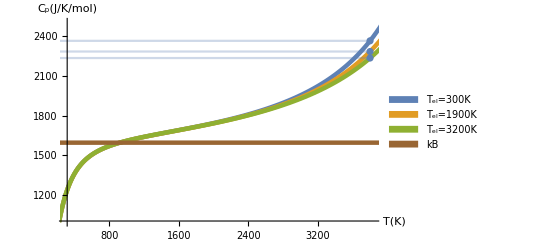

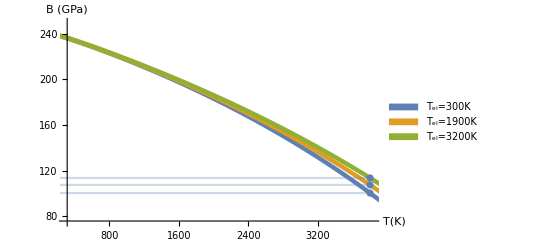

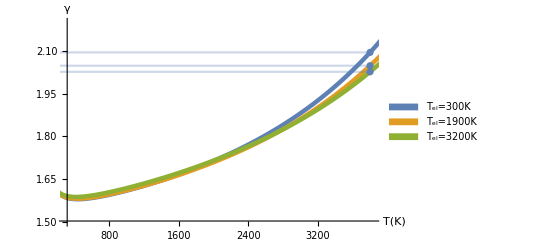

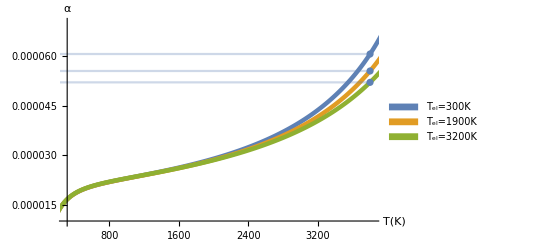

```mathematica
kbplot=Plot[8.3144621*64*3,{T,1,4000},PlotLegends->SwatchLegend[{"kB"}],PlotStyle->{Brown,Thickness[0.008]}];
Show[ListPlot[{qhaData[[1]],qhaData[[5]],qhaData[[9]]},PlotLegends->SwatchLegend[{"T_el=300K","T_el=1900K","T_el=3200K"}],AxesLabel->{"T(K)","C_p(J/K/mol)"},PlotStyle->Thickness[0.008],Joined->True,PlotRange->{{300,3829},{1000,2500}}],kbplot,horizontalListPlotFill[ListPlot[{qhaData[[1]][[381]],qhaData[[5]][[381]],qhaData[[9]][[381]]}]]]

Show[ListPlot[{qhaData[[2]],qhaData[[6]],qhaData[[10]]},PlotLegends->SwatchLegend[{"T_el=300K","T_el=1900K","T_el=3200K"}],AxesLabel->{"T(K)","B (GPa)"},PlotStyle->Thickness[0.008],Joined->True,PlotRange->{{300,3829},{75,250}}],horizontalListPlotFill[ListPlot[{qhaData[[2]][[381]],qhaData[[6]][[381]],qhaData[[10]][[381]]}]]]

Show[ListPlot[{qhaData[[3]],qhaData[[7]],qhaData[[11]]},PlotLegends->SwatchLegend[{"T_el=300K","T_el=1900K","T_el=3200K"}],AxesLabel->{"T(K)","γ"},PlotStyle->Thickness[0.008],Joined->True,PlotRange->{{300,3829},{1.5,2.2}}],horizontalListPlotFill[ListPlot[{qhaData[[3]][[381]],qhaData[[7]][[381]],qhaData[[11]][[381]]}]]]



Show[ListPlot[{qhaData[[4]],qhaData[[8]],qhaData[[12]]},PlotLegends->SwatchLegend[{"T_el=300K","T_el=1900K","T_el=3200K"}],AxesLabel->{"T(K)","α"},PlotStyle->Thickness[0.008],Joined->True,PlotRange->{{300,3829},{0.00001,0.00007}}],horizontalListPlotFill[ListPlot[{qhaData[[4]][[381]],qhaData[[8]][[381]],qhaData[[12]][[381]]}]]]
```

```mathematica
qhaData[[2]][[397]]
```

{3960.,91.2603}

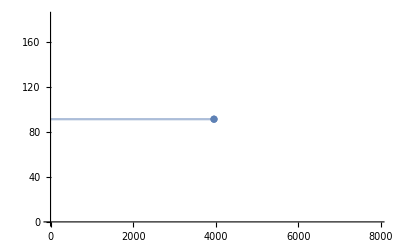

```mathematica
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};

horizontalListPlotFill[ListPlot[{qhaData[[2]][[397]]}]]
```

```mathematica
qhaData[[2]][[381]]
```

{3800.,100.3811428391963}